Comprensión del lenguaje natural

Anteriormente se vio cómo utilizar ctrl= para ingresar una entrada en lenguaje natural. Ahora se describirá cómo establecer funciones que puedan comprender el lenguaje natural.

Interpreter es la clave para mucho de este tema. Se le dice al intérprete qué tipo de cosa se desea obtener y, entonces, este toma cualquier cadena de caracteres que se le den y trata de interpretarla.

Interprete la cadena "nyc" como ciudad:

```mathematica
Interpreter["City"]["nyc"]
```

New York City

“The big apple” es un apodo de la ciudad de Nueva York:

```mathematica
Interpreter["City"]["the big apple"]
```

New York City

Interprete la cadena "hot pink" como color:

```mathematica
Interpreter["Color"]["hot pink"]
```

RGBColor[1., 0.4117647058823529, 0.7058823529411764]

Interpreter convierte lenguaje natural en expresiones de Wolfram Language con las que se pueden efectuar procesos de cómputo. He aquí un ejemplo relacionado con montos de dinero.

Interprete diversos montos de dinero:

```mathematica
Interpreter["CurrencyAmount"][{"4.25 dollars","34 russian rubles","5 euros","85 cents"}]
```

{4.25 $,34  руб,5 €,85 ¢}

Calcule el total en dólares, haciendo la conversión con los tipos de cambio del momento:

```mathematica
Total[{Quantity[4.25, "USDollars"],Quantity[34, "RussianRubles"],Quantity[5, "Euros"],Quantity[85, "USCents"]}]
```

11.07 $

Aquí está otro ejemplo, que se refiere a ubicaciones.

Interpreter da la ubicación geográfica de la Casa Blanca:

```mathematica
Interpreter["Location"]["White House"]
```

GeoPosition[{38.8977,-77.0366}]

Puede funcionar también a partir de un domicilio:

```mathematica
Interpreter["Location"]["1600 Pennsylvania Avenue, Washington, DC"]
```

GeoPosition[{38.8977,-77.0366}]

Interpreter maneja centenares de diferentes tipos de objetos.

Interprete los nombres de universidades (de cuál “U of I” se trate depende de la localización geográfica):

```mathematica
Interpreter["University"][{"Harvard","Stanford","U of I"}]
```

{Harvard University,Stanford University,University of Illinois at Urbana-Champaign}

Interprete los nombres de sustancias químicas:

```mathematica
Interpreter["Chemical"][{"H2O","aspirin","CO2","wolfram"}]
```

{water,aspirin,carbon dioxide,tungsten}

Interprete nombres de animales y, luego, obtenga sus imágenes:

```mathematica
EntityValue[Interpreter["Animal"][{"cheetah","tiger","elephant"}],"Image"]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

Interpreter interpreta cadenas completas de caracteres. TextCases, en cambio, intenta elegir, de una cadena, los casos que se piden.

Elija los sustantivos en una porción de texto:

```mathematica
TextCases["A sentence is a linguistic construct","Noun"]
```

{sentence,construct}

Elija cantidades de dinero:

```mathematica
TextCases["Choose between $5, €5 and ¥5000","CurrencyAmount"]
```

{$5,€5,¥5000}

Se puede usar TextCases para elegir tipos particulares de cosas en una porción de texto. Por ejemplo, aquí se eligen los casos que sean nombres de países en cierto artículo de Wikipedia.

Genere la nube de palabras de los nombres de países que aparecen en el artículo de Wikipedia sobre la Unión Europea:

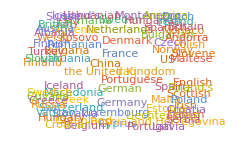

```mathematica
WordCloud[TextCases[WikipediaData["EU"],"Country"]]
```

TextStructure muestra la estructura completa de una porción de texto.

Vea cómo puede analizarse sintácticamente en unidades gramaticales una oración en inglés:

```mathematica
TextStructure["You can do so much with the Wolfram Language."]
```

You
Pronoun
Noun Phrase  can
Verb  do
Verb  so
Adverbmuch
Adverb
Adverb Phrase  with
Preposition  the
DeterminerWolfram
Proper NounLanguage
Proper Noun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence

Representación alternativa en forma de gráfico:

```mathematica
TextStructure["You can do so much with the Wolfram Language.","ConstituentGraphs"]
```

{-Graphics-}

WordList[ ] da una lista de palabras comunes del inglés. WordList["Noun"], etc. da las listas de palabras que pueden usarse como partes particulares del lenguaje.

Busque los 20 primeros casos de la lista de verbos comunes del inglés:

```mathematica
Take[WordList["Verb"],20]
```

{aah,abandon,abase,abash,abate,abbreviate,abdicate,abduct,abet,abhor,abide,abjure,ablate,abnegate,abolish,abominate,abort,abound,abrade,abridge}

Es muy fácil estudiar algunas de las propiedades de las palabras. Aquí se presentan los histogramas que comparan las distribuciones de la longitud de sustantivos, verbos y adjetivos en la lista de palabras comunes del inglés.

Haga los histogramas de las longitudes de los sustantivos, verbos y adjetivos en inglés:

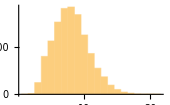
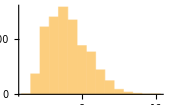
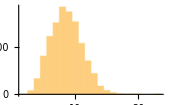

```mathematica
Histogram[StringLength[WordList[#]]]&/@{"Noun","Verb","Adjective"}
```

Hasta el momento se ha considerado solo el inglés. Sin embargo, Wolfram Language puede también manejarse con otros idiomas. Por ejemplo, WordTranslation traduce palabras.

Traduzca “hello” al francés:

```mathematica
WordTranslation["hello","French"]
```

{bonjour,hello,holà,ohé}

Traduzca al coreano:

```mathematica
WordTranslation["hello","Korean"]
```

{여보세요,안녕하세요}

Traduzca al coreano y después translitere al alfabeto inglés:

```mathematica
Transliterate[WordTranslation["hello","Korean"]]
```

{yeoboseyo,annyeonghaseyo}

Si se quiere hacer la comparación entre muchas lenguas diferentes, se da la opción All para la lengua en WordTranslation. Como resultado se obtiene una asociación que da las traducciones a diferentes idiomas, listados más o menos de acuerdo con su grado de uso en el mundo.

De la traducción de “hello” en las 5 lenguas más usadas en el mundo:

```mathematica
Take[WordTranslation["hello",All],5]
```

<|Mandarin→{表示問候的叫聲},Hindi→{हलो,नमस्ते},Spanish→{buenos días,hola},Russian→{привет,приветствие,Здравствуйте},Indonesian→{halo}|>

Se toman ahora las 100 lenguas de uso más común, y se encuentra el primer caracter de la primera de las traducciones que hay para “hello”. Ahora se muestra la nube de palabras, que muestra que en esas lenguas la “h” es la que aparece como inicial más frecuente en las traducciones de “hello”.

Considerando los 100 primeros lenguajes, cree una nube de palabras con las letras iniciales de la palabra “hello”:

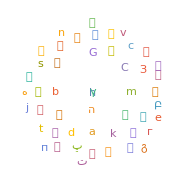

```mathematica
WordCloud[Values[StringTake[First[#],1]&/@Take[WordTranslation["hello",All],100]]]
```

Vocabulario

Interpreter["tipo"] |   | especifica una función para interpretar lenguaje natural 
TextCases["texto","tipo"] |   | encuentra los casos de un tipo dado de objeto en texto 
TextStructure["texto"] |   | encuentra la estructura gramatical de texto 
WordTranslation["palabra","lengua"] |   | traduce una palabra a otra lengua

"15 Exercises Available" | "Get Started »"

Use Interpreter para encontrar la ubicación de la torre Eiffel. »

| Expected output: |  
  | GeoPosition[{48.8583,2.29444}] |

Use Interpreter para encontrar una universidad a la que se suele llamar “U of T”. »

| Expected output: |  
  | "University of Toronto" |

Use Interpreter para encontrar las sustancias químicas a las que se refieren como C2H4, C2H6 y C3H8. »

| Expected output: |  
  | {"ethylene","ethane","propane"} |

Use Interpreter para interpretar la fecha “20140108”. »

| Expected output: |  
  | "Wed 8 Jan 2014" |

Encuentre aquellas universidades que puedan ser llamadas como “U of X”, donde x es cualquier letra del alfabeto. »

| Expected output: |  
  | {"University of Birjand","University of Chicago","The University of Edinburgh","University of Georgia","University of Houston","University of Illinois at Urbana-Champaign","University of Lethbridge","University of Michigan-Ann Arbor","University of Phoenix-Online Campus","University of Regina","University of Saskatchewan","University of Toronto"} |

Busque cuáles de los nombres de las capitales de los estados de EE. UU. pueden interpretarse como títulos de películas (usar CommonName para obtener las versiones de los nombres de entidades como cadenas de caracteres). »

| Expected output: |  
  | {"Phoenix","Lincoln","Honolulu","Annapolis","Expedition: Bismarck","Providence","Nashville","Olympia","Madison"} |

Busque cuáles nombres de ciudades son permutaciones de las letras a, i, l y m. »

| Expected output: |  
  | {"Lima","Ilam","Milah","Mali"} |

Haga la nube de palabras de los nombres de países que aparecen en el artículo de Wikipedia sobre “gunpowder”. »

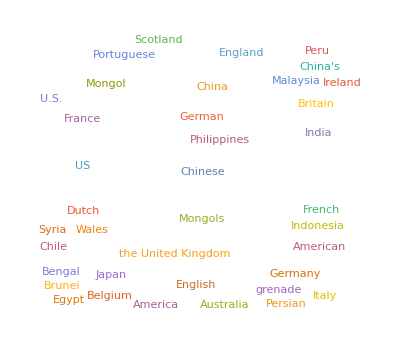
| Sample expected output: |  
  | -Graphics- |

Busque todos los sustantivos en “She sells seashells by the sea shore.” »

| Expected output: |  
  | {"seashells","sea","shore"} |

Use TextCases para encontrar el número de sustantivos, verbos y adjetivos en los primeros 1000 caracteres del artículo de Wikipedia sobre “computers”. »

| Expected output: |  
  | {42,29,18} |

Encuentre la estructura gramatical de la primera oración del artículo de Wikipedia sobre “computers”. »

| Sample expected output: |  
  |  " " " ""A"
"Determiner""computer"
"Noun"
"Noun Phrase" " ""is"
"Verb" " " " ""a"
"Determiner""general-purpose"
"Adjective""device"
"Noun"
"Noun Phrase" " " " ""that"
"Determiner"
"Wh-Noun Phrase" " " " ""can"
"Verb" " ""be"
"Verb" " ""programmed"
"Verb" " " " ""to"
"Preposition" " ""carry"
"Verb" " ""out"
"Particle"
"Particle" " " " ""a"
"Determiner""set"
"Noun"
"Noun Phrase" " ""of"
"Preposition" " ""arithmetic"
"Noun""or"
"Conjunction""logical"
"Adjective""operations"
"Noun"
"Noun Phrase"
"Prepositional Phrase"
"Noun Phrase"
"Verb Phrase"
"Verb Phrase"
"Clause" " ""automatically"
"Adverb"
"Adverb Phrase"
"Verb Phrase"
"Verb Phrase"
"Verb Phrase"
"Clause"
"Clause"
"Noun Phrase"
"Verb Phrase""."
"Punctuation"
"Sentence" |

Encuentre los 10 sustantivos más comunes en ExampleData[{"Text","AliceInWonderland"}]. »

| Expected output: |  
  | {"door","voice","time","way","moment","thing","head","table","round","nothing"} |

Muestre la representación del grafo de comunidades de la estructura textual de la primera oración del artículo de Wikipedia sobre “language”. »

| Sample expected output: |  
  | -Graphics- |

Haga la lista de los totales de sustantivos, verbos, adjetivos y adverbios que existen en WordList en inglés. »

| Expected output: |  
  | {25133,6671,11520,3199} |

Genere la lista de las traducciones de los números 2 al 9 al francés. »

| Expected output: |  
  | {"deux","trois","quatre","cinq","six","sept","huit","neuf","dix"} |

Preguntas y respuestas

Qué tipos posibles de intérpretes hay?

Es una lista larga. Consulte la documentación o evalúe $InterpreterTypes para ver la lista.

¿Se necesita tener una conexión a la red para usar Interpreter?

En casos sencillos, tales como fechas o divisas básicas, no se requiere. Pero sí es necesaria para trabajar con entradas de lenguaje natural completo.

Al decir “4 dollars”, ¿cómo puede saberse si se trata de dólares estadounidenses o de otro tipo?

Puede intentar deducirse de qué tipo de dólares se está hablando con base en la ubicación geográfica.

¿Puede el Interpreter trabajar con lenguaje natural arbitrario?

Si algo puede expresarse en Wolfram Language, entonces Interpreter debería poder interpretarlo. Interpreter["SemanticExpression"] toma cualquier entrada e intenta entender su significado, de tal modo que pueda obtener una expresión de Wolfram Language que lo capture. En esencia, lo que hace sería la primera etapa de lo que hace Wolfram|Alpha.

¿Pueden incorporarse intérpretes hechos por el usuario?

Sí. GrammarRules permite construir una gramática propia, usando cualesquier intérpretes que se quiera.

¿Puede buscarse el significado de una palabra?

WordDefinition da las definiciones de diccionario.

Dada una palabra, ¿puede encontrarse a qué categoría gramatical corresponde?

PartOfSpeech da todas las categorías gramaticales a las que puede corresponder una palabra. Así, para “fish” da sustantivo y nombre. Cuál de ellas sea la correcta depende de cómo se esté usando la palabra en una oración, y de esto se encarga TextStructure.

Además de palabras, ¿pueden traducirse oraciones completas?

TextTranslation lo hace con algunos lenguajes y, generalmente, recurre a algún servicio externo.

¿Qué lenguajes maneja WordTranslation?

Puede traducir una buena cantidad de palabras de algunos centenares de los lenguajes más comunes. Y traduce al menos unas cuantas palabras de más de un millar de lenguajes. LanguageData da información acerca de más de 10 000 lenguajes.

Notas técnicas

TextStructure requiere de un texto gramaticalmente completo, pero Interpreter usa muchas técnicas diferentes para trabajar también con fragmentos de texto.

Al usar ctrl= se puede resolver interactivamente la ambigüedad en la entrada. Con Interpreter hay que hacerlo programáticamente, usando la opción AmbiguityFunction.

Para explorar más

Guía para intérpretes de lenguaje natural en Wolfram Language »